# Plotting Functions

## Basic Exercises

### Question Subsection

Plot the Heaviside function, H(x), form -1 to 1.

#### Hint

Use the built-in function HeavisideTheta[x_].

#### Solution

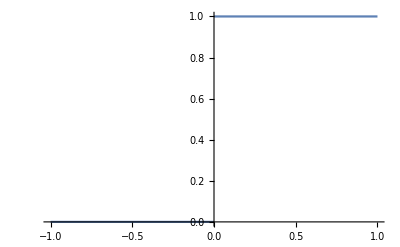

```mathematica
Plot[HeavisideTheta[x],{x,-1,1}]
```

### Question Subsection

Plot the Gamma function, Γ(x), from -5 to 5. Add labels to your plot. Change the style of the plot so that the curve is red and thick.

#### Hint

Use the built-in function Gamma[x_].

#### Solution

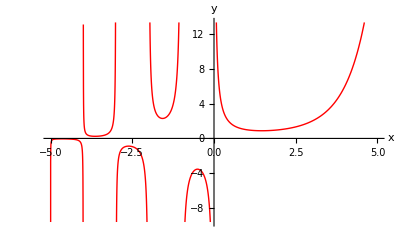

```mathematica
Plot[Gamma[x],{x,-5,5}, AxesLabel->{x,y}, PlotStyle->{Red,Thick}]
```

### Question Subsection

Plot the Bessel function of the first kind, J_n(x), from -5 to 5, for n=0,1,2, on the same plot. Add labels and legends to your plot.

#### Hint

Use the built-in function BesselJ[n_,x_].

#### Solution

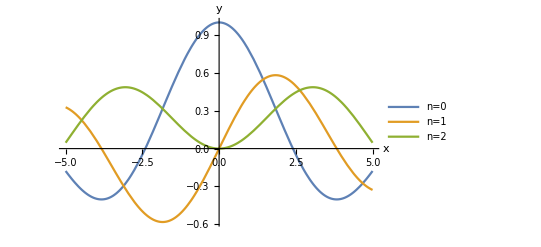

```mathematica
Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x]},{x,-5,5},AxesLabel->{x,y},PlotLegends->{"n=0","n=1","n=2"}]
```

### Question Subsection

Plot the Legendre Polynomials, P_n(x), of order n from -1 to 1, for n=5,8,12, on the same plot. Draw a background grid and a frame, and change the style of the plot to red and thick.

#### Hint

Use the built-in function LegendreP[n_,x_].
Use options GridLines and Frame.

#### Solution

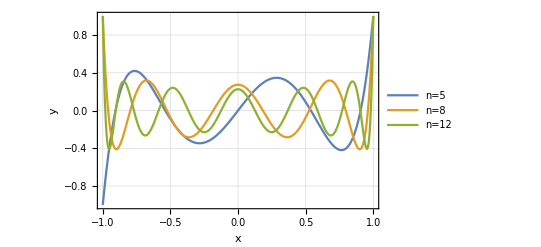

```mathematica
Plot[{LegendreP[5,x],LegendreP[8,x],LegendreP[12,x]},{x,-1,1},AxesLabel->{x,y},PlotLegends->{"n=5","n=8","n=12"},GridLines->Automatic,Frame->True]
```

### Question Subsection

Reproduce the plots form the last two exercises side by side. Include labels, legends, background grid and frame. Make the image size large. Label each plot.

#### Hint

Use GraphicsRow. 
Use PlotLabel.

#### Solution

```mathematica
GraphicsRow[{Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x]},{x,-5,5},AxesLabel->{x,y},PlotLegends->{"n=0","n=1","n=2"},GridLines->Automatic,Frame->True,PlotLabel->"BesselJ"],Plot[{LegendreP[5,x],LegendreP[8,x],LegendreP[12,x]},{x,-1,1},AxesLabel->{x,y},PlotLegends->{"n=5","n=8","n=12"},GridLines->Automatic,Frame->True,PlotLabel->"Legendre"]},ImageSize->Large]
```

-Graphics-